```mathematica
ClearAll["Global`*"]
```

## Figure 3 Mathematica File

This code will reproduce Fig 3 of the main text. Panels were combined and labels were added to the figure using PowerPoint. Note that the below notation uses types i and j;  in the main text, these are substituted with h Hawk and d Dove.

### Define Functions

```mathematica
(*This function gives the invasion funtion for type i. It uses the analytical solutions for the 1-consumer-1-resource equilibria for type i and calculates the key quantities from equation 10 *)
InvasionCondition[taui_,tauj_,ai_,aj_,e_,m_,k_,r_,βi_,βj_]:=Module[{Si,Hi,RiI,ωji,ωij,Pj,RjE,invasionCondition},

(*Define the expressions*)
Si=r (ai k (e-m taui)-m (m taui+1))/(ai m (1+(k r ai taui)/(βi+m)));(*Searcher at Equilibrium for i*)
Hi=(r taui (ai (e k-k m taui)-m (1+m taui)))/(ai ((m r taui (1+m taui))/(m+βi)+e-m taui));(*Handler at Equilibrium for i*)
RiI=m (m taui+1) (1+(k r ai taui)/(βi+m))/(ai (e+m taui ((r (m taui+1))/(βi+m)-1))); (*Resource at Equilibrium for i*)
ωji=(βi+m)/(βi+βj+2 m); (*prob j wins contest*)
ωij=(βj+m)/(βi+βj+2 m); (*prob i wins contest*)
Pj=1/(1+((aj Hi)/(βi+βj+2 m))+((ai Si)/(1/tauj+m) (ωij+aj(Hi+RiI)/(βi+βj+2 m))));  (* Cost of interference*)
RjE=(m (m tauj+1))/(aj (e-m tauj));  (*Exploitative Rstar for j*)

(*Calculate the invasion condition*)
invasionCondition=Pj (RiI+ωji Hi)-RjE; (*Note that in contrast to equation 10, we have subtracted RjE from each side to give Subscript[I, j]-Subscript[E, ji]. j invades if Subscript[I, j]-Subscript[E, ji]>0*)
(*Return the result*)
invasionCondition]

(*This function calculates Subscript[β, 0] (the golden star in Fig. 3; see Supplementary Materials G for a derivation). We center the plots around Subscript[β, 0]*)
OptimalBeta[τ_,e_,m_,a_,k_,r_]:=Re[(m^2 τ (3-r τ)-m (-1+2 e+r τ)+√m √(1+m τ) √(m+4 a e k r τ+m r^2 τ^2-2 m r τ (1+2 a k τ)+m^2 τ (-1+r τ)^2))/(2 (e-m τ))];

(*This function inputs the analytical solution for the 1-consumer-1-resource equilibrium (for type i) and the Subscript[I, j] term from equation 11. It then takes the |Log(Subscript[I, j])|, as explained in the main text  *)
IjTerm[taui_,tauj_,ai_,aj_,e_,m_,k_,r_,βi_,βj_]:=Module[{Si,Hi,RiI,ωji,ωij,Pj,RjE,RiE,Ij},

(*Define the expressions*)
Si=r (ai k (e-m taui)-m (m taui+1))/(ai m (1+(k r ai taui)/(βi+m)));(*Searcher at Equilibrium for i*)
Hi=(r taui (ai (e k-k m taui)-m (1+m taui)))/(ai ((m r taui (1+m taui))/(m+βi)+e-m taui));(*Handler at Equilibrium for i*)
RiI=m (m taui+1) (1+(k r ai taui)/(βi+m))/(ai (e+m taui ((r (m taui+1))/(βi+m)-1))); (*Resource at Equilibrium for i*)
ωji=(βi+m)/(βi+βj+2 m); (*prob j wins contest*)
ωij=(βj+m)/(βi+βj+2 m); (*prob i wins contest*)
Pj=1/(1+((aj Hi)/(βi+βj+2 m))+((ai Si)/(1/tauj+m) (ωij+aj(Hi+RiI)/(βi+βj+2 m))));  (* Cost of interference*)
RjE=(m (m tauj+1))/(aj (e-m tauj));  (*Exploitative Rstar for j*)
RiE=(m (m taui+1))/(ai (e-m taui));  (*Exploitative Rstar for j*)

(*Calculate the Ij term*)
Ij=Pj (RiI/RiE+ωji Hi/RiE); 
(*Return the result*)
Abs[Log[Ij]]];
(*This function calculates the exploitative Rstar ratio,Subscript[E, ji]=Subscript[R, j,E]/Subscript[R, i,E]. It then takes |Log(Subscript[E, ji])|, as explained in the main text  *)
EjiTerm[taui_,tauj_,ai_,aj_,e_,m_,k_,r_,βi_,βj_]:=Module[{RjE,RiE,Eji},
(*Define the expressions*)
RjE=(m (m tauj+1))/(aj (e-m tauj));  (*Exploitative Rstar for j*)
RiE=(m (m taui+1))/(ai (e-m taui));  (*Exploitative Rstar for j*)
(*Calculate the invasion condition*)
Eji=RjE/RiE; (*Exploitative Rstar Ratio*)
(*return |Log(Subscript[E, ji])|*)
Abs[Log[Eji]]];
(*This function calculates the ratio of interference Rstar values, Subscript[R, j,I]/Subscript[R, i,I] *)
InterferenceRstarRatio[taui_,tauj_,ai_,aj_,e_,m_,k_,r_,βi_,βj_]:=Module[{RjI,RiI,RstarRatio},
(*Define the expressions*)
RjI=m (m tauj+1) (1+(k r aj tauj)/(βj+m))/(aj (e+m tauj ((r (m tauj+1))/(βj+m)-1))); (*Interference Rstar for j*)
RiI=m (m taui+1) (1+(k r ai taui)/(βi+m))/(ai (e+m taui ((r (m taui+1))/(βi+m)-1))); (*Interference Rstar for i*)
(*Calculate the invasion condition*)
RstarRatio=RjI/RiI; (* Calculate Subscript[R, j,I]/Subscript[R, i,I]*)
(*return Subscript[R, j,I]/Subscript[R, i,I]*)
RstarRatio]
```

## Set Parameters

Here, we set the parameters used in the below plots. Parameters are the same as those used in Fig. 3 in the main text.

```mathematica
tau=1; (*handling time (same for both types in Fig. 3)*)
a = .1; (*attack rate (same for both types in Fig. 3)*)
e=.035; (*conversion efficiency*)
m=.015; (*baseline mortality*)
k=250; (*resource capacity*)
r=.26; (*resource renewal rate*)

(* Parameter that scales plots *)
SCALE = 10 ;
```

## Run Numerics for Plots

```mathematica
(*This RegionPlot will draw the lines (black boundaries) of the plate; delinates coexistence and exclusion*)
PlotBoundaries=RegionPlot[{InvasionCondition[tau,tau,a,a,e,m,k,r,βd,βh]>0&&
βd>βh,InvasionCondition[tau,tau,a,a,e,m,k,r,βh,βd]>0&&
βd>βh},
{βh,OptimalBeta[tau,e,m,a,k,r]/SCALE,OptimalBeta[tau,e,m,a,k,r]*SCALE},
{βd,OptimalBeta[tau,e,m,a,k,r]/SCALE,OptimalBeta[tau,e,m,a,k,r]*SCALE},
PlotTheme->"Marketing",
PlotPoints->50,
MaxRecursion->4,
GridLines->None,
PlotStyle->{Directive[Red,Opacity[0]],Directive[Blue,Opacity[0]]},BoundaryStyle->Directive[Black,Thickness[.012]],FrameTicksStyle->Directive[Black,FontSize-> 22],FrameTicks->{{{Round[OptimalBeta[tau,e,m,a,k,r],.1]/SCALE,Round[OptimalBeta[tau,e,m,a,k,r],.1]/SCALE},{Round[OptimalBeta[tau,e,m,a,k,r],.1],Round[OptimalBeta[tau,e,m,a,k,r],.1]},{Round[OptimalBeta[tau,e,m,a,k,r],.1]*SCALE,Round[OptimalBeta[tau,e,m,a,k,r],.1]*SCALE}},{{Round[OptimalBeta[tau,e,m,a,k,r],.1]/SCALE,Round[OptimalBeta[tau,e,m,a,k,r],.1]/SCALE},{Round[OptimalBeta[tau,e,m,a,k,r],.1],Round[OptimalBeta[tau,e,m,a,k,r],.1]},{Round[OptimalBeta[tau,e,m,a,k,r],.1]*SCALE,Round[OptimalBeta[tau,e,m,a,k,r],.1]*SCALE}}},FrameStyle->Directive[Black,AbsoluteThickness[2.5]],ScalingFunctions->{"Log","Log"},PlotLegends->None];

(*This RegionPlot will draw the region in which Hawk-Dove coexistence occurs:|Log(Subscript[I, d])| > |Log(Subscript[E, dh])|, |Log(Subscript[I, h])| > |Log(Subscript[E, dh])|*)
HawkDoveCoexistenceRegion=RegionPlot[{IjTerm[tau,tau,a,a,e,m,k,r,βh,βd]>EjiTerm[tau,tau,a,a,e,m,k,r,βh,βd]&&
IjTerm[tau,tau,a,a,e,m,k,r,βd,βh]>EjiTerm[tau,tau,a,a,e,m,k,r,βd,βh]&&
InvasionCondition[tau,tau,a,a,e,m,k,r,βh,βd]>0&&
InvasionCondition[tau,tau,a,a,e,m,k,r,βd,βh]>0&&
βd>βh,
βh>βd},
{βh,OptimalBeta[tau,e,m,a,k,r]/SCALE,OptimalBeta[tau,e,m,a,k,r]*SCALE},{βd,OptimalBeta[tau,e,m,a,k,r]/SCALE,OptimalBeta[tau,e,m,a,k, r]*SCALE},PlotTheme->"Marketing",
PlotPoints->50,
MaxRecursion->4,
PlotLegends->None,
GridLines->None,
PlotStyle->{Directive[Cyan,Opacity[0.4]],Directive[White,Opacity[1]]},BoundaryStyle-> {Gray,Thickness[.0075]},FrameTicksStyle->{{Directive[FontOpacity->0,FontSize-> 22],Automatic},{Directive[Black,FontSize-> 22],Automatic}},FrameTicks->{{Round[OptimalBeta[tau,e,m,a,k, r],.1]/SCALE,Round[OptimalBeta[tau,e,m,a,k, r],.1],Round[OptimalBeta[tau,e,m,a,k, r],.1]*SCALE},{Round[OptimalBeta[tau,e,m,a,k, r],.1]/SCALE,Round[OptimalBeta[tau,e,m,a,k, r],.1],Round[OptimalBeta[tau,e,m,a,k, r],.1]*SCALE}},FrameStyle->Directive[Black,AbsoluteThickness[2.5]],
ScalingFunctions->{"Log","Log"}];

(*This RegionPlot will draw the region in which Dove excludes the Hawk *)
DoveWinsRegion=RegionPlot[{IjTerm[tau,tau,a,a,e,m,k,r,βd,βh]>EjiTerm[tau,tau,a,a,e,m,k,r,βd,βh]&&
InvasionCondition[tau,tau,a,a,e,m,k,r,βd,βh]<0&&
βh<βd,
βh>βd},
{βh,OptimalBeta[tau,e,m,a,k, r]/SCALE,OptimalBeta[tau,e,m,a,k, r]*SCALE},{βd,OptimalBeta[tau,e,m,a,k, r]/SCALE,OptimalBeta[tau,e,m,a,k, r]*SCALE},PlotTheme->"Marketing",
PlotPoints->50,
MaxRecursion->4,
PlotLegends->None,
GridLines->None,
PlotStyle->{Directive[Orange,Opacity[0.4]],Directive[White,Opacity[1]]},BoundaryStyle-> {Gray,Thickness[.0075]},FrameTicksStyle->{{Directive[FontOpacity->0,FontSize-> 22],Automatic},{Directive[Black,FontSize-> 22],Automatic}},FrameTicks->{{Round[OptimalBeta[tau,e,m,a,k, r],.1]/SCALE,Round[OptimalBeta[tau,e,m,a,k, r],.1],Round[OptimalBeta[tau,e,m,a,k, r],.1]*SCALE},{Round[OptimalBeta[tau,e,m,a,k, r],.1]/SCALE,Round[OptimalBeta[tau,e,m,a,k, r],.1],Round[OptimalBeta[tau,e,m,a,k, r],.1]*SCALE}},FrameStyle->Directive[Black,AbsoluteThickness[2.5]],ScalingFunctions->{"Log","Log"}];

(*This RegionPlot will draw the region in which Hawk excludes the Dove *)
HawkWinsRegion=RegionPlot[{IjTerm[tau,tau,a,a,e,m,k,r,βh,βd]>EjiTerm[tau,tau,a,a,e,m,k,r,βh,βd]&&
InvasionCondition[tau,tau,a,a,e,m,k,r,βh,βd]<0&&
βh<βd,
βh>βd},
{βh,OptimalBeta[tau,e,m,a,k, r]/SCALE,OptimalBeta[tau,e,m,a,k, r]*SCALE},{βd,OptimalBeta[tau,e,m,a,k, r]/SCALE,OptimalBeta[tau,e,m,a,k, r]*SCALE},PlotTheme->"Marketing",
PlotPoints->50,
MaxRecursion->4,
PlotLegends->None,
GridLines->None,
PlotStyle->{Directive[Green,Opacity[0.4]],Directive[White,Opacity[1]]},BoundaryStyle-> {Gray,Thickness[.0075]},FrameTicksStyle->{{Directive[FontOpacity->0,FontSize-> 22],Automatic},{Directive[Black,FontSize-> 22],Automatic}},FrameTicks->{{Round[OptimalBeta[tau,e,m,a,k, r],.1]/SCALE,Round[OptimalBeta[tau,e,m,a,k, r],.1],Round[OptimalBeta[tau,e,m,a,k, r],.1]*SCALE},{Round[OptimalBeta[tau,e,m,a,k, r],.1]/SCALE,Round[OptimalBeta[tau,e,m,a,k, r],.1],Round[OptimalBeta[tau,e,m,a,k, r],.1]*SCALE}},FrameStyle->Directive[Black,AbsoluteThickness[2.5]],
ScalingFunctions->{"Log","Log"}]; 

(*This DensityPlot will draw Subscript[R, j,I]/Subscript[R, i,I] as a functino Subscript[β, d] and Subscript[β, h] *)
RstarPlot=DensityPlot[InterferenceRstarRatio[tau,tau,a,a,e,m,k,r,βd,βh]&&βd>βh,
{βh,OptimalBeta[tau,e,m,a,k, r]/SCALE,OptimalBeta[tau,e,m,a,k, r]*SCALE},
{βd,OptimalBeta[tau,e,m,a,k, r]/SCALE,OptimalBeta[tau,e,m,a,k, r]*SCALE},
PlotRange->{{OptimalBeta[tau,e,m,a,k, r]/(SCALE*1.05),OptimalBeta[tau,e,m,a,k, r]*SCALE},{OptimalBeta[tau,e,m,a,k, r]/SCALE,OptimalBeta[tau,e,m,a,k, r]*SCALE},{1,12}},
PlotTheme->"Marketing",
PlotPoints->50,
MaxRecursion->4,
AspectRatio->1,BoundaryStyle-> Directive[Black,Thickness[.012]],
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize-> 22],Automatic},{Directive[Black,FontSize-> 22],Automatic}},
FrameTicks->{{{Round[OptimalBeta[tau,e,m,a,k, r],.1]/SCALE,Round[OptimalBeta[tau,e,m,a,k, r],.1],Round[OptimalBeta[tau,e,m,a,k, r],.1]*SCALE},None},{{Round[OptimalBeta[tau,e,m,a,k, r],.1]/SCALE,Round[OptimalBeta[tau,e,m,a,k, r],.1],Round[OptimalBeta[tau,e,m,a,k, r],.1]*SCALE},None}},ColorFunction->ColorData[{"RedBlueTones","Reverse"}],
FrameStyle->Directive[Black,AbsoluteThickness[3.5]],ScalingFunctions->{"Log10","Log10","Log10"},
PlotLegends->Placed[Automatic,Right],
Epilog->{Thickness[.01],Dashed,Line[{{Log10[OptimalBeta[tau,e,m,a,k, r]],Log10[OptimalBeta[tau,e,m,a,k, r]]},{Log10[OptimalBeta[tau,e,m,a,k, r]],Log10[OptimalBeta[tau,e,m,a,k, r]*SCALE]}}],Line[{{Log10[OptimalBeta[tau,e,m,a,k, r]/SCALE],Log10[OptimalBeta[tau,e,m,a,k, r]]},{Log10[OptimalBeta[tau,e,m,a,k, r]],Log10[OptimalBeta[tau,e,m,a,k, r]]}}]}];
```

## Make Plots

The below code shows each figure; figures were copied and pasted into PowerPoint, where they were labeled.

```mathematica
Panel4A = Show[PlotBoundaries,HawkDoveCoexistenceRegion,DoveWinsRegion,HawkWinsRegion,PlotBoundaries]
```

-Graphics-

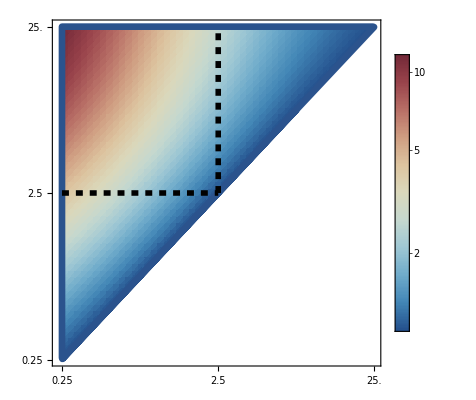

```mathematica
RstarPlot
```